```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\HILL\Documents\GitHub\thesis\figures\spectro

```mathematica
fontSize=30;
```

### Plot a Lorentzian profiles of the surface, plot1

```mathematica
A=800000;
a=80;
b=0.0007;
λ0=512;
js={60,100,120,140,180};
surf=Function[{x,y},A(Exp[-b(x-90)^2]+Exp[-b(x-90-70)^2])/((y-512)^2+a^2)];
height=Function[x,A(Exp[-b(x-90)^2]+Exp[-b(x-90-70)^2])/((λ0-512)^2+a^2)](*Half height at position j, same as surf but without (u-λ0)^2*);
```

```mathematica
plot1=ParametricPlot3D[
Table[{j,u,surf[j,u]},{j,js}],{u,0,1024}
,FaceGrids->{{{0,0,-1},{Range[0,256,32],Range[0,1024,32]}}}
,FaceGridsStyle->Directive[Gray,Dashed]
,PlotRange->{{0,256},{0,1024},{0,130}}
,ViewPoint->{10,40,10}
,ViewVertical->{0,0,9}
,Ticks->None
,Axes->True
,Boxed->False
,AxesOrigin->{0,0,0}
,AxesStyle->Table[{Thick,Black},{j,3}]
,AxesLabel->Table[Style[j,fontSize,Black,Bold],{j,{"Spatial coordinate\n[px]","Wavelength [nm]","Intensity"}}]
,ImageSize->960
]
```

-Graphics3D-

#### Labels and arrows of FWHM

```mathematica
Δλ=Text[Style["Δλ",Bold,Black,fontSize],{Last[js],λ0,height[Last[js]]/2-22}];
xlabel=Text[Style["Spatial coordinate\n[px]",Bold,Black,fontSize],{256,0,0}];
ylabel=Text[Style["λ [nm]",Bold,Black,fontSize],{0,1024,0}];
zlabel=Text[Style["Intensity",Bold,Black,fontSize],{0,0,130}];
```

```mathematica
ω=0.015;(*arrow size*)
arrows=Table[
{Arrowheads[{-ω,ω}],
Arrow[{{j,λ0-a,height[j]/2},{j,λ0+a,height[j]/2}}]},
{j,js}
];
```

### Plot the Lorentzians with the arrows and labels, plot2:

```mathematica
faceGridPositions={{{0,0,-1},{Range[0,256,32],Range[0,1024,32]}}};
plot2=Show[{
Graphics3D[xlabel],
Graphics3D[ylabel],
Graphics3D[zlabel],
Graphics3D[arrows],
Graphics3D[Δλ],
ParametricPlot3D[
Table[{j,u,surf[j,u]},{j,js}],{u,0,1024}]
},
Axes->True,
AxesStyle->Thick,
Boxed->False
,Ticks->{{512,256},None,None}
,AxesOrigin->{0,0,0}
,PlotRange->{{0,256},{0,1024},{0,130}}
,ViewPoint->{10,40,10}
,ViewVertical->{0,0,9}
,ImageSize->960
,FaceGrids->faceGridPositions
,FaceGridsStyle->Directive[Gray,Dashed]
]
```

-Graphics3D-

For a lorentzian of the form used here, f(x)=1/((x-X)^2+a^2):
The half maximum is at x→X-a, x→X+a, i.e., fwhm =2a.
f(X-a)=f(X+a)=1/(2 a^2).

### Plot the mesh of the surface, plot3:

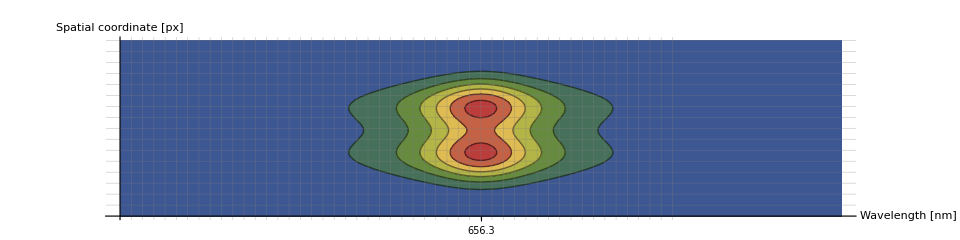

```mathematica
r=120;
b=0.0007;
plot3=ContourPlot[
surf[y,x],{x,0,1024},{y,0,256},
ColorFunction->"DarkRainbow",
AspectRatio->1/4,
Axes->True,
Frame->False,
AxesStyle->Table[{Thick,Black},{j,2}],
Ticks->{{{512,"656.3",0.02}},None},
TicksStyle->Directive["Label", fontSize],
GridLines->{Range[0,1024,16],Range[0,256,16]},
AxesLabel->Table[Style[j,fontSize,Black,Bold],{j,{"Wavelength [nm]","Spatial coordinate\n[px]"}}],
PlotRange->{{0,1024},{0,256},All}
,Epilog->{ 
Inset[Style[Framed[Style["256×1024 pixels",fontSize,Black,Bold,Background->White],FrameMargins->3]],{810,300}] 
}
,ImageSize->960
,PlotRangeClipping->False
,ImagePadding->All
]
```

### The Parabola plot

Piecewise[{{10+ⅇ^(0.285714 (-14+x)), x<10}, {10+1/70 (-15+x)^2, 10<x<20}, {10+ⅇ^(-0.285714 (-16+x)), x>16}, {0, True}}]

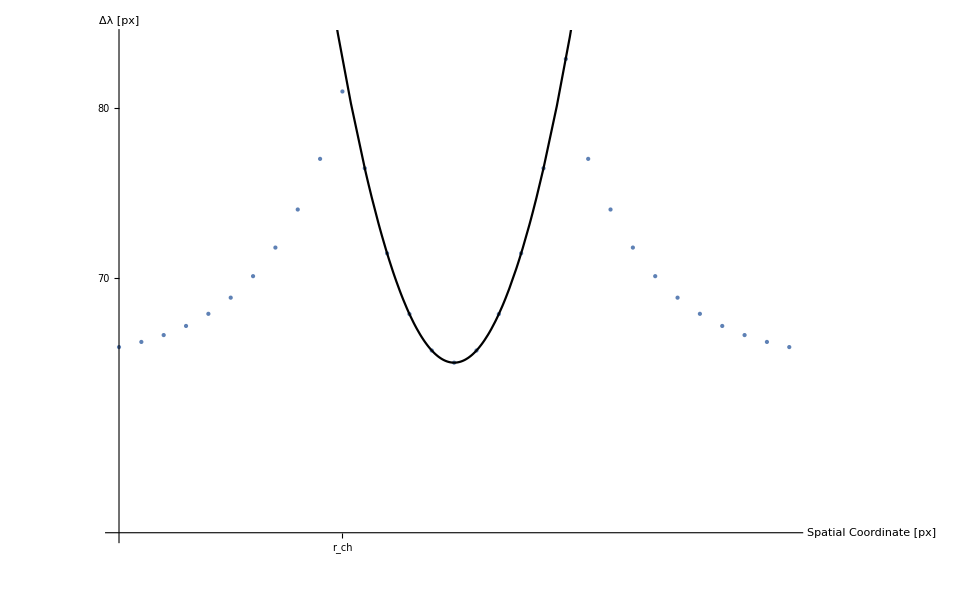

```mathematica
d=15;
l=1;
α=3.5;
p=Piecewise[{
{ⅇ^(+(x-(d-l))/α)+10,x<d-5},
{(x-d)^2/70+10,d-5<x<d+5},
{ⅇ^(-(x-(d+l))/α)+10,x>d+l}}]
plot4=Show[
ListPlot[Thread[
{Range[0,30],
Flatten[
{Table[Evaluate[p⟦1,1,1⟧],{x,0,10}],Table[Evaluate[p⟦1,2,1⟧],{x,11,20}],Table[Evaluate[p⟦1,3,1⟧],{x,21,30}]}
]}
]
,
PlotRange->{9.8,10.38},
PlotStyle->PointSize[Large],
(*GridLines->{{{5,{Dashed,Black,Thick}},{15,{Dashed,Black,Thick}}},None},*)
AxesLabel->{Style["Spatial\nCoordinate [px]",Bold,fontSize],Style["Δλ [px]",Bold,fontSize]},
TicksStyle->Directive["Label", 20],
Ticks->{{{31,256,0.02,Black},{10,"r_ch",{0.58,0.02},{Black,Dashed,Thick}}(*,{15,"r_ch",{0.58,0.02},{Black,Dashed,Thick}}*)}, {{10.3,80,0.02,Black},{10.1,70,0.02,Black}}},
AxesStyle->Table[{Black,Thick},{j,2}]
,
ImageSize->960
]
,
Plot[Evaluate[p⟦1,2,1⟧],{x,0,30},PlotStyle->Black]
]
```

### Plot the 3 plots in a grid

```mathematica
Import["blue arrows-down.pdf"]⟦1⟧
```

-Graphics-

```mathematica
Import["blue arrows-right.pdf"]⟦1⟧
```

-Graphics-

```mathematica
Grid[{{plot3, Null, Null}, {-Graphics-, Null, Null}, {plot2, -Graphics-, plot4}}]
```

-Graphics- |  | 
-Graphics- |  | 
-Graphics3D- | -Graphics- | -Graphics-

```mathematica
Export["spectra_analysis.pdf",Grid[{{plot3, Null, Null}, {-Graphics-, Null, Null}, {plot2, -Graphics-, plot4}}]]
```

spectra_analysis.pdf

```mathematica
SystemOpen["spectra_analysis.pdf"]
```

```mathematica
SystemOpen["spectra_analysis.pdf"]
```

```mathematica
SystemOpen["spectra_analysis.pdf"]
```

```mathematica
Export["spectra_analysis.png",Grid[{{plot3, Null, Null}, {-Graphics-, Null, Null}, {plot2, -Graphics-, plot4}}]]
```

spectra_analysis.png

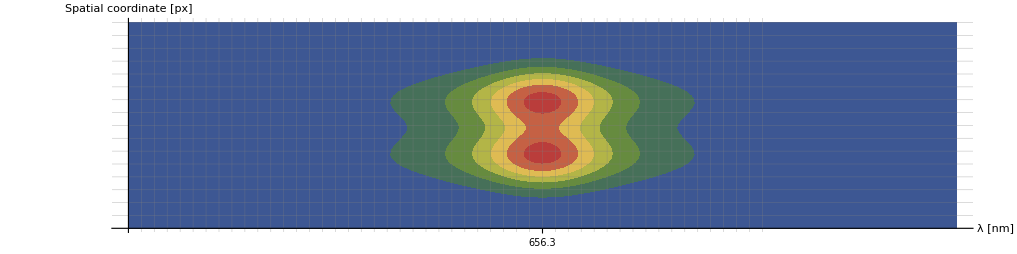

```mathematica
g2=ContourPlot[surf[y,x],{x,0,1024},{y,0,256},
ColorFunction->"DarkRainbow",
ContourStyle->None,
AspectRatio->1/4,
Axes->True,
AxesStyle->Table[{Thick,Black},{j,2}],
Ticks->{{{512,"656.3",0.02}},None},
TicksStyle->Directive["Label", fontSize,Bold,Black],
GridLines->{Range[0,1024,16],Range[0,256,16]},
AxesLabel->Table[Style[j,fontSize,Black,Bold],{j,{"λ [nm]","Spatial coordinate\n[px]"}}],
Frame->False,
PlotRange->{{0,1024},{0,256},All}
(*,ImageSize->Tiny*)
]
```